# Calculation 3D lattice

October 2001, Markus Greiner; updated 2006 Immanuel Bloch; extended 2009 Ulrich Schneider

## Atomic and lattice parameters

```mathematica
c:= 2.99792458×10^8;
```

```mathematica
h:=6.6260755×10^-34;
```

```mathematica
hbar:=h/(2π);
```

```mathematica
LatticeWavelength:=725.6×10^-9;
```

```mathematica
λ=LatticeWavelength;
```

```mathematica
wLattice:=160×10^-6;
```

```mathematica
DipoleWavelength:=1030×10^-9;
```

```mathematica
wlongDipole:=150×10^-6;
```

```mathematica
wshortDipole:=50×10^-6;
```

```mathematica
mp:= 1.6726231×10^-27;
```

```mathematica
mRb:=87*mp;
```

```mathematica
mK:=39*mp;
```

```mathematica
a0=0.529177×10^-10;
```

```mathematica
kB:=1.3806504*10^-23;
```

```mathematica
ErecoilRb[λ_]:=h^2/(2mRb λ^2);(*in Joule*)
```

```mathematica
ErecoilK[λ_]:=h^2/(2mK λ^2);
```

```mathematica
ErecoilRbLattice:=ErecoilRb[LatticeWavelength]
```

```mathematica
ErecoilKLattice:=ErecoilK[LatticeWavelength]
```

```mathematica
N[ErecoilKLattice/h]
```

9646.49

Lattice wavevector

```mathematica
k:=2π/LatticeWavelength;
```

Recoil energies

Streulänge K-K (9/2,-9/2) (9/2,-7/2)

```mathematica
aK:=174 a0;
```

```mathematica
aRb := 100 a0;
```

## Periodic Dipole Potential

Dipole potential

```mathematica
Subscript[V, 0]:=(ℏ Subscript[Γ, d]^2)/(8 Δ)Subscript[I, stdwave]/Subscript[I, sat];
```

1D standing wave: Imax=4 I_0

```mathematica
Subscript[I, stdwave]:=3.5 Subscript[I, gauss];
```

Peak intensity

```mathematica
Subscript[I, gauss]:=P 2/(π Subscript[w, 0]^2);
```

Definition: recoil energy

k

```mathematica
k:=(2π)/LatticeWavelength;
```

V_0 in recoil

Assumption: linewidth average for both lines

```mathematica
Subscript[Γ, d]:=(Subscript[Γ, D1]+Subscript[Γ, D2])/2;
```

```mathematica
ℏ:=hbar;
```

Assumption: detuning average for both lines

```mathematica
Δ:=2π c(1/Subscript[λ, lat]-2/(Subscript[λ, D1]+Subscript[λ, D2]));
```

Experimental values (λ_lat lattice wavelength; w_0 lattice laser beam waist):

## Approximative Solutions -- illustration only, do not use

### Tunneling Matrix Element in Units of the Recoil Energy

```mathematica
Japprox[V0_]:=4/(√π)(V0)^(3/4)Exp[-2 V0^(1/2)];
```

```mathematica
N[Japprox[5]]*ErecoilKLattice/h
```

831.491

```mathematica
N[Japprox[7]]
```

0.048892

### Interaction Matrix Element in Units of the Recoil Energy

```mathematica
Uapprox[V0_,ascatt_]:=√(8/π)k ascatt (V0)^(3/4);
```

```mathematica
Uapprox[10,aK]
```

0.715489

```mathematica
N[ErecoilK[LatticeWavelength]/h]
```

9646.49

### Interaction Energy for 40 K

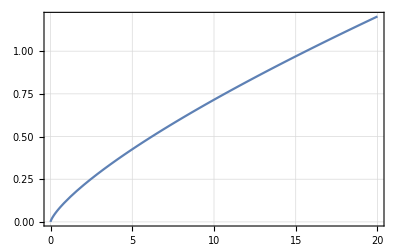

```mathematica
Plot[Uapprox[V0,174 a0],{V0,0,20},Frame->True,GridLines->Automatic]
```

### Ratio Interaction to Tunneling Energy for 40K

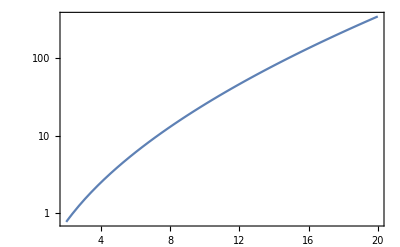

```mathematica
LogPlot[Uapprox[V0,140 a0]/Japprox[V0],{V0,2,20},Frame->True,GridLines->Automatic]
```

## Band Structure Calculation

#### Hamiltonian in discrete basis - in units of Er

```mathematica
Hij[V0_,q_,i_,j_]:=If[i==j,(2i+q)^2+V0/2,If[Abs[i-j]==1,-1/4 V0,0]];
MatrixSize=5; (* Matrixsize=n  equals FO=n+1*)
FO=MatrixSize+1; (* used later on*)
H[V0_,q_]:=Table[Hij[V0,q,i,j],{i,-MatrixSize,MatrixSize},{j,-MatrixSize,MatrixSize}]
MatrixForm[H[V0,q]]
```

((-10+q)^2+V0/2 | -V0/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-V0/4 | (-8+q)^2+V0/2 | -V0/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -V0/4 | (-6+q)^2+V0/2 | -V0/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -V0/4 | (-4+q)^2+V0/2 | -V0/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -V0/4 | (-2+q)^2+V0/2 | -V0/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -V0/4 | q^2+V0/2 | -V0/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -V0/4 | (2+q)^2+V0/2 | -V0/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -V0/4 | (4+q)^2+V0/2 | -V0/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -V0/4 | (6+q)^2+V0/2 | -V0/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -V0/4 | (8+q)^2+V0/2 | -V0/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -V0/4 | (10+q)^2+V0/2)

#### Get energy values for certain crystal momentum q and lattice depth V (all in Er); Sorted in ascending order (lowest energy comes first)

```mathematica
eigenvals[V_,q_]:=Sort[N[Eigenvalues[H[V,q]]]]
```

```mathematica
eigenvals[0,0]
```

{0.,4.,4.,16.,16.,36.,36.,64.,64.,100.,100.}

#### (2-1) Energy difference between first energy band and lowest energy band

```mathematica
eigenvals[10,1][[2]]-eigenvals[10,1][[1]]
```

4.57226

#### (3-2) Energy difference between third energy band and second energy band

```mathematica
eigenvals[10,0][[3]]-eigenvals[10,0][[2]]
```

2.12057

#### (3-1) Energy difference between third energy band and second energy band

```mathematica
eigenvals[20,0][[3]]-eigenvals[20,0][[1]]
```

13.2492

#### Band Structure

```mathematica
Animate[ListLinePlot[Transpose[Table[Sort[N[Re[Eigenvalues[H[Vlat,q]]]]],{q,0,1,0.01}]][[{1,2,3,4}]],PlotRange->{0,20},Frame->True],{Vlat,0,20,1}]
```

#### Bandwidth: Energy difference between lowest q=0 and q=1 state:

```mathematica
Bandwidth[V_]:=Sort[Chop[N[Eigenvalues[H[V,1]]]]][[1]]-
Sort[Chop[N[Eigenvalues[H[V,0]]]]][[1]]
```

```mathematica
Bandwidth[1]
```

0.773468

#### Tunnelling energy = Bandwidth/4

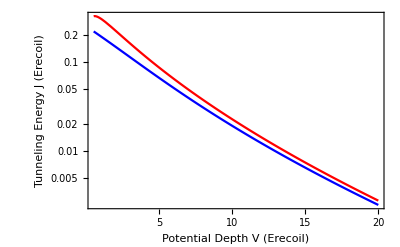

```mathematica
LogPlot[{Bandwidth[v]/4,Japprox[v]},{v,0.5,20},GridLines->Automatic,Frame->True,FrameLabel->{"Potential Depth V (Erecoil)","Tunneling Energy J (Erecoil)"},PlotStyle->{Blue,Red}]
```

```mathematica
Table[{V0,Bandwidth[V0]/4*ErecoilKLattice/h},{V0,4,14}]//MatrixForm
```

(4 | 831.744
5 | 637.178
6 | 490.894
7 | 380.702
8 | 297.306
9 | 233.792
10 | 185.084
11 | 147.463
12 | 118.199
13 | 95.28
14 | 77.2138)

```mathematica
FirstToThird[V_]:=Sort[Chop[N[Eigenvalues[H[V,0]]]]][[3]]-
Sort[Chop[N[Eigenvalues[H[V,0]]]]][[1]]
```

```mathematica
FirstToThird[20]*ErecoilKLattice/h
```

127808.

```mathematica
FirstToSecond[V_]:=Sort[Chop[N[Eigenvalues[H[V,0]]]]][[2]]-
Sort[Chop[N[Eigenvalues[H[V,0]]]]][[1]]
```

```mathematica
FirstToSecond[15]*ErecoilKLattice/h
```

65613.8

```mathematica
EP=1/2 mK(2π 40)^2(80*10^-6)^2/h
```

19899.2

## Calculating the Bloch functions for 10Er lattice depth

Stepsize for different q

```mathematica
qstep=0.1
```

0.1

Table of eigenvectors

```mathematica
t=Abs[N[Eigensystem[H[10,0]]][[2]]];
```

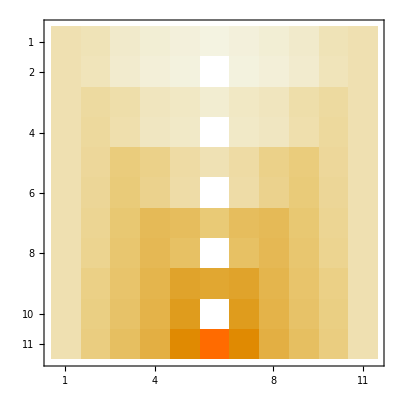

```mathematica
MatrixPlot[t]
```

```mathematica
(*This list contains only the lowest Eigenstate for every q*)
```

```mathematica
EVtemp=Table[Sort[Transpose[Chop[N[Eigensystem[H[10,q0]]]]]] [[1,2]],{q0,-1,1,qstep}];
```

Normalizing the eigenvectors

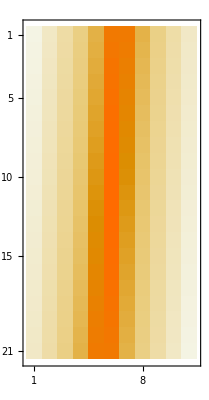

```mathematica
(*not needed for lowest band, eigenstates are already normalised, but doesn't hurt*)
EV=Table[EVtemp[[Round[(q0+1)/qstep+1]]]/Norm[EVtemp[[Round[(q0+1)/qstep+1]]],2]*Sign[EVtemp[[Round[(q0+1)/qstep+1],FO]]],{q0,-1,1,qstep}];
EV //MatrixForm;
MatrixPlot[EV]
```

Creating table of Bloch functions ψ(x) for different q

```mathematica
(* A list of Bloch waves for discrete qs*)
```

```mathematica
Table[{2n,n,n+FO},{n,-FO+1,FO-1}]//MatrixForm
```

(-10 | -5 | 1
-8 | -4 | 2
-6 | -3 | 3
-4 | -2 | 4
-2 | -1 | 5
0 | 0 | 6
2 | 1 | 7
4 | 2 | 8
6 | 3 | 9
8 | 4 | 10
10 | 5 | 11)

```mathematica
ψ[x_]=Table[Sum[Exp[I (q0+2n)k x]*EV[[Round[(q0+1)/qstep+1],n+FO]],{n,-FO+1,FO-1}],{q0,-1,1,qstep}];
```

```mathematica
Re[ψ[x][[2]]]
```

Re[0.719731 ⅇ^((0.-7.79337×10^6 ⅈ) x)+0.655933 ⅇ^((0.+9.52523×10^6 ⅈ) x)+0.175586 ⅇ^((0.-2.5112×10^7 ⅈ) x)+0.143032 ⅇ^((0.+2.68438×10^7 ⅈ) x)+0.0169078 ⅇ^((0.-4.24306×10^7 ⅈ) x)+0.0127848 ⅇ^((0.+4.41624×10^7 ⅈ) x)+0.00085201 ⅇ^((0.-5.97491×10^7 ⅈ) x)+0.000609791 ⅇ^((0.+6.1481×10^7 ⅈ) x)+0.00002622 ⅇ^((0.-7.70677×10^7 ⅈ) x)+0.0000179586 ⅇ^((0.+7.87996×10^7 ⅈ) x)+5.42236×10^-7 ⅇ^((0.-9.43863×10^7 ⅈ) x)]

Bloch functions for q=0 and q=1

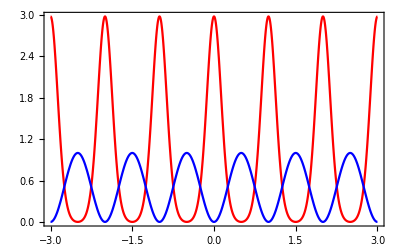

```mathematica
Plot[{Re[ψ[x*LatticeWavelength/2][[1]]]^2 ,Sin[(x*LatticeWavelength/2)*2*π/(LatticeWavelength)]^2},{x,-3,3},PlotRange->All,Frame->True,PlotStyle->{Red,Blue,Blue,Blue,Black}]
```

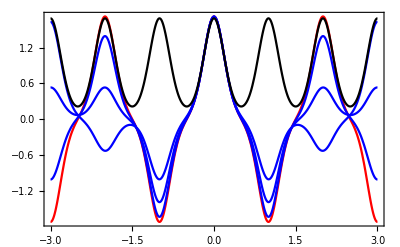

```mathematica
Plot[{Re[ψ[x*LatticeWavelength/2][[1]]] ,Re[ψ[x*LatticeWavelength/2][[2]]] ,Re[ψ[x*LatticeWavelength/2][[3]]],Re[ψ[x*LatticeWavelength/2][[4]]],Re[ψ[x*LatticeWavelength/2][[11]]]},{x,-3,3},PlotRange->All,Frame->True,PlotStyle->{Red,Blue,Blue,Blue,Black}]
```

... squared

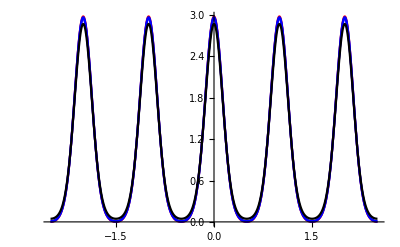

```mathematica
Plot[{Abs[ψ[x*LatticeWavelength/2][[1]]]^2,Abs[ψ[x*LatticeWavelength/2][[3]]]^2,Abs[ψ[x*LatticeWavelength/2][[4]]]^2,Abs[ψ[x*LatticeWavelength/2][[11]]]^2},{x,-2.5,2.5},PlotRange->All,PlotStyle->{Red,Blue,Blue,Black}]
```

## Calculating Wannier function at 10Er

Wannier Function is sum over Bloch functions of lowest band with different q, normalized
Notice: q=1 and q=-1 is only counted half in order not to count double

```mathematica
(* First, sum over all, then subtract 0.5 times the -1 and 1 ones, agrees with Oberthaler except for /(2/qstep)*√(k/π); but normalisation is ok.*)
w[x_]=(Plus@@ψ[x]-0.5(ψ[x][[1]]+ψ[x][[2/qstep+1]]))/(2/qstep)*√(k/π);
```

Plot of the wannier function

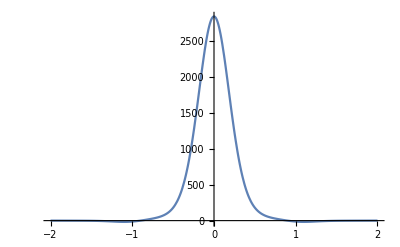

```mathematica
Plot[Chop[w[x*LatticeWavelength/2]],{x,-2,2},PlotRange->All]
```

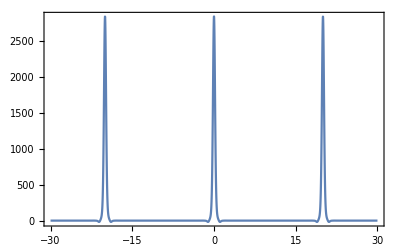

```mathematica
Plot[Chop[w[x*LatticeWavelength/2]],{x,-30,30},PlotRange->All,Frame->True,Axes->False]
```

```mathematica
(*Fourier theorem: We use only a finite number of Bloch states .-> Wannier are periodic*)
```

Onsite interaction energy UK

```mathematica
U=(4π hbar^2 aK)/(mK ErecoilKLattice)NIntegrate[Re[w[x]]^4,{x,-10^-6,10^-6}]^3
```

0.544952

#### Check Normalization

```mathematica
NIntegrate[Re[w[x]]^2,{x,-1*10^-6,1*10^-6}]
```

1.

```mathematica
Module[{dx=0.05},dx*LatticeWavelength/2*Sum[w[x*LatticeWavelength/2]^2,{x,-8,8,dx}]]
```

1.-1.84411×10^-19 ⅈ

## Calculating/Exporting Wannier function at lower lattice depth

```mathematica
V0tmp=1;
```

```mathematica
EVtemp=Table[Sort[Transpose[Chop[N[Eigensystem[H[V0tmp,q0]]]]]] [[1,2]],{q0,-1,1,qstep}];
EV=Table[EVtemp[[Round[(q0+1)/qstep+1]]]/Norm[EVtemp[[Round[(q0+1)/qstep+1]]],2]*Sign[EVtemp[[Round[(q0+1)/qstep+1],FO]]],{q0,-1,1,qstep}];
(*Bloch*)ψ[x_]=Table[Sum[Exp[I (q0+2n)k x]*EV[[Round[(q0+1)/qstep+1],n+FO]],{n,-FO+1,FO-1}],{q0,-1,1,qstep}];
W[x_]:=(Plus@@ψ[x]-0.5(ψ[x][[1]]+ψ[x][[2/qstep+1]]))/(2/qstep)*√(k/π);
```

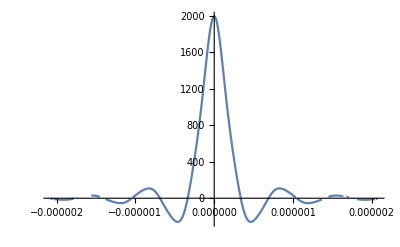

```mathematica
Plot[W[x],{x,-7*LatticeWavelength,7*LatticeWavelength},PlotRange->All]
```

```mathematica
T=Table[{x//N,Re[W[x*LatticeWavelength]]},{x,-7,7,1/100}];
```

```mathematica
(*Export["U:\\Dokumente\\work\\mathematica\\T10.dat",T]*)
```

## Wannier for different potential depth

### Wannier for 1Er -- 50Er

Stepsize for different q

```mathematica
qstep=0.1;
```

Create table of Wannier functions

```mathematica
wtab=Table[
EVtemp=Table[Sort[Transpose[Chop[N[Eigensystem[H[V0,q0]]]]]] [[1,2]],{q0,-1,1,qstep}];
EV=Table[EVtemp[[Round[(q0+1)/qstep+1]]]/Norm[EVtemp[[Round[(q0+1)/qstep+1]]],2]*Sign[EVtemp[[Round[(q0+1)/qstep+1],FO]]],{q0,-1,1,qstep}];
ψ[x_]=Table[Sum[Exp[I (q0+2n)k x]*EV[[Round[(q0+1)/qstep+1],n+FO]],{n,-FO+1,FO-1}],{q0,-1,1,qstep}];
(Plus@@ψ[x]-0.5(ψ[x][[1]]+ψ[x][[2/qstep+1]]))/(2/qstep)*√(k/π)
,{V0,1,50}];
```

One might approximate the functions

```mathematica
wtabi=Table[Module[{wj},wj=wtab[[V0]];FunctionInterpolation[Re[wj],{x,-2*10^-6,2*10^-6}]],{V0,1,21}];
```

FunctionInterpolation::ncvb: FunctionInterpolation failed to meet the prescribed accuracy and precision goals after 6 recursive bisections near x = {-2.×10^-6}. Continuing to refine elsewhere.

FunctionInterpolation::ncvb: FunctionInterpolation failed to meet the prescribed accuracy and precision goals after 6 recursive bisections near x = {-1.96875×10^-6}. Continuing to refine elsewhere.

FunctionInterpolation::ncvb: FunctionInterpolation failed to meet the prescribed accuracy and precision goals after 6 recursive bisections near x = {-1.90625×10^-6}. Continuing to refine elsewhere.

General::stop: Further output of FunctionInterpolation::ncvb will be suppressed during this calculation.

Comparison: Wannier functions and gauss functions (harmonic potential) for different potential depths:

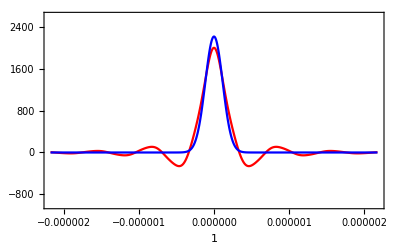
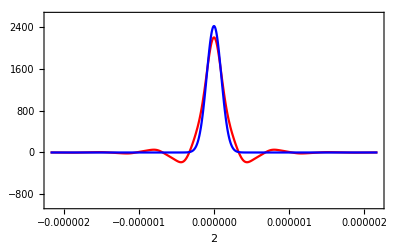
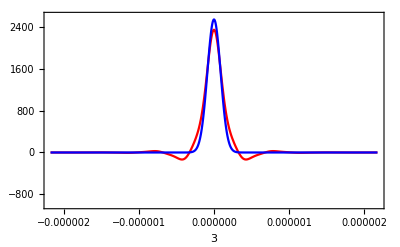
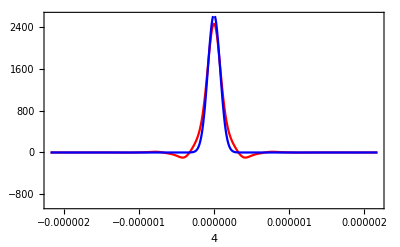
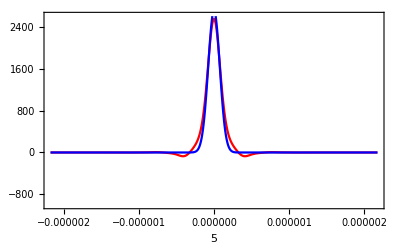
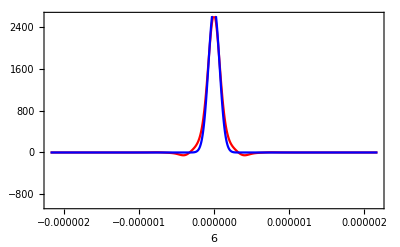
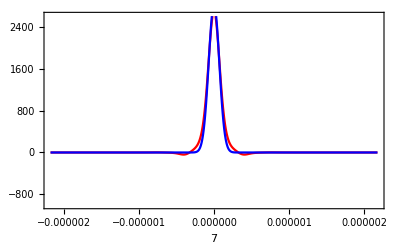
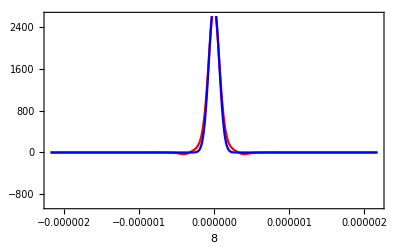

```mathematica
Table[Module[{wj},wj=wtab[[V0]];Plot[{Re[wj],((k^2 √V0)/π)^(1/4)Exp[-1/2 x^2 k^2 √V0]},{x,-3 LatticeWavelength,3LatticeWavelength},PlotRange->{-1000,2600},Frame->True,Axes->False,FrameLabel->V0,PlotStyle->{Red,Blue}]],{V0,1,10}]
```

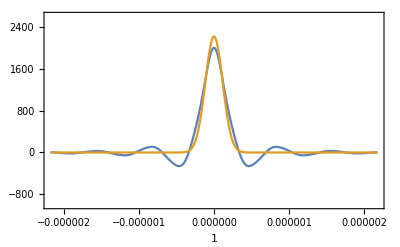

```mathematica
Module[{wj},wj=wtab[[1]];Plot[{Re[wj],((k^2 √1)/π)^(1/4)Exp[-1/2 x^2 k^2 √1]},{x,-3 LatticeWavelength,3LatticeWavelength},PlotRange->{-1000,2600},Frame->True,Axes->False,FrameLabel->1]]
```

### Onsite interaction matrix element U, calculated with Wannier and gauss

```mathematica
(* In units of the recoil energy!!, U formular is ok*)
```

```mathematica
Uw=Table[Module[{wj},wj=wtab[[V0]];(4π hbar^2 150 a0)/(mK ErecoilKLattice)NIntegrate[Re[wj]^4,{x,-4*10^-6,4*10^-6}]^3],{V0,1,20}];
```

```mathematica
Ug=Table[Uapprox[V0,150 a0],{V0,1,20}];
```

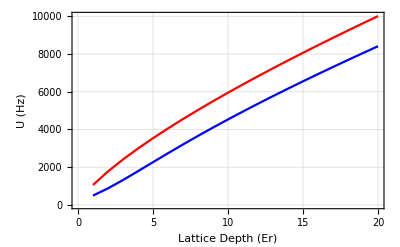

```mathematica
ListPlot[{Uw*ErecoilKLattice/h,Ug*ErecoilKLattice/h},Joined->True,Frame->True,GridLines->Automatic,FrameLabel->{"Lattice Depth (Er)","U (Hz)"},PlotStyle->{Blue,Red}]
```

Interpolation for U(V)

```mathematica
U=Interpolation[Transpose[{Table[n,{n,1,20}],Uw}]];
```

U/(6J) plotted versus V, all in units of recoil energy

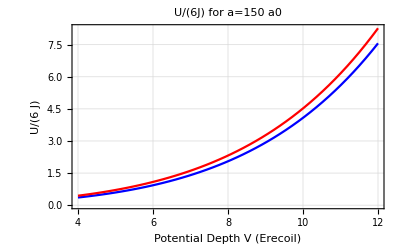

```mathematica
Plot[{U[v]/(Bandwidth[v]/4*6),Uapprox[v,150 a0]/(6*Japprox[v])},{v,4,12},GridLines->Automatic,Frame->True,PlotLabel->"U/(6J) for a=150 a0",FrameLabel->{"Potential Depth V (Erecoil)","U/(6  J)"},PlotStyle->{Blue,Red}]
```

```mathematica
Module[{v=10},N[{U[v],(Bandwidth[v]/4*6),U[v]/(Bandwidth[v]/4*6),Uapprox[v,150 a0],(6*Japprox[v]),Uapprox[v,150 a0]/(6*Japprox[v])}]]
```

{0.469786,0.11512,4.08083,0.616801,0.136432,4.52093}

```mathematica
N[(Bandwidth[v]/4)/6 /.v->10]
```

-0.232034

```mathematica
Bandwidth[10]
```

0.0767468

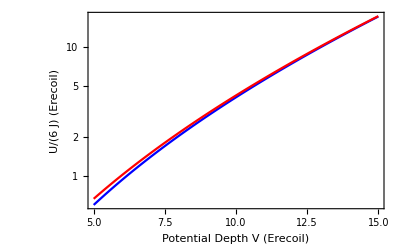

```mathematica
LogPlot[{U[v]/(Bandwidth[v]/4*6),Uapprox[v,140 a0]/(6*Japprox[v])},{v,5,15},GridLines->Automatic,Frame->True,FrameLabel->{"Potential Depth V (Erecoil)","U/(6  J) (Erecoil)"},PlotStyle->{Blue,Red}]
```

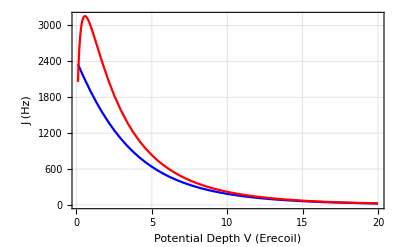

```mathematica
Plot[{Bandwidth[v]/4*ErecoilKLattice/h,Japprox[v]*ErecoilKLattice/h},{v,0.1,20},PlotStyle->{Blue,Red},Frame->True,Axes->False,FrameLabel->{"Potential Depth V (Erecoil)","J (Hz) "},GridLines->Automatic]
```

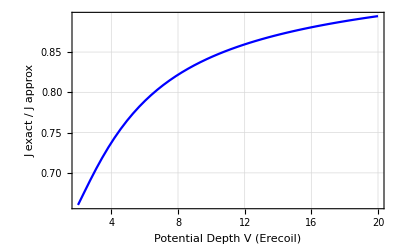

```mathematica
Plot[{Bandwidth[v]/4/Japprox[v]},{v,2,20},PlotStyle->{Blue},Frame->True,Axes->False,FrameLabel->{"Potential Depth V (Erecoil)","J exact / J approx"},GridLines->Automatic]
```

```mathematica
Ug[[8]]*(ErecoilKLattice/h)
```

5033.05

```mathematica
Uw[[8]]*(ErecoilKLattice/h)
```

3658.94

```mathematica
Uapprox[8,140 a0]*(ErecoilKLattice/h)
```

4697.52

```mathematica
Table[{v,(Bandwidth[v]/4)},{v,1,50}];
```

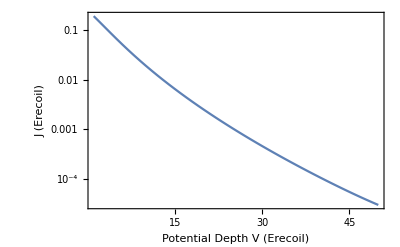

```mathematica
LogPlot[Interpolation[%][v],{v,1,50},GridLines->Automatic,Frame->True,FrameLabel->{"Potential Depth V (Erecoil)","J (Erecoil)"}]
```

### Calculate J by integrating over Wanniers

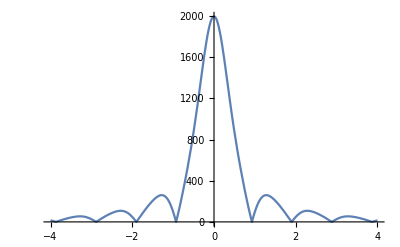

```mathematica
Plot[Abs[wtabi[[1]][x*LatticeWavelength/2]],{x,-4,4},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-2.17671×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

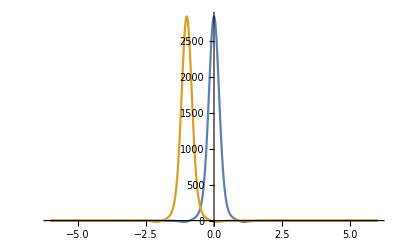

```mathematica
Plot[{wtabi[[10]][x*LatticeWavelength/2],wtabi[[10]][(x+1)*LatticeWavelength/2]},{x,-6,6},PlotRange->All]
```

```mathematica
w[V0_,x_]:=wtabi[[V0]][x]
```

```mathematica
norm[V0_]:=NIntegrate[w[V0,x]*w[V0,x],{x,-6*LatticeWavelength/2,6*LatticeWavelength/2}]
```

```mathematica
norm[10]
```

0.999989

```mathematica
V[V0_,x_]:=ErecoilKLattice*V0*Sin[x*2*π/LatticeWavelength]^2;
```

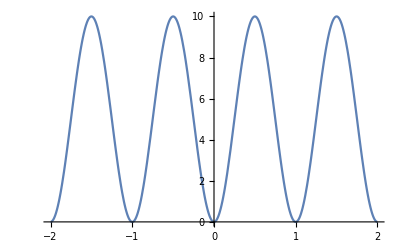

```mathematica
Plot[V[10,x*LatticeWavelength/2]/ErecoilKLattice,{x,-2,2}]
```

```mathematica
w0=wtabi[[10]]
```

InterpolatingFunction[…]

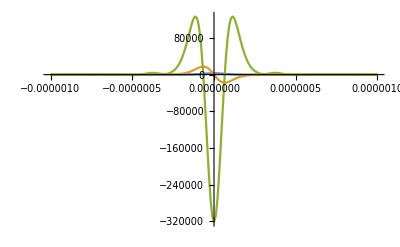

```mathematica
Plot[{w0[x],w0'[x]*LatticeWavelength,w0''[x]*LatticeWavelength^2},{x,-10^-6,10^-6},PlotRange->All]
```

```mathematica
diffw[V0_,x_]:=Module[{w=wtabi[[V0]]},w''[x]];
```

```mathematica
diffw[10,0]
```

-6.10082×10^17

```mathematica
right[V0_,x_]:=-hbar^2/(2 mK)diffw[V0,x]+V[V0,x]*w[V0,x]
```

```mathematica
right[10,10^-7]
```

1.95784×10^-26

```mathematica
ClearAll[J];
J[V0_]:=J[V0]=NIntegrate[w[V0,x+LatticeWavelength/2]*right[V0,x],{x,-6*LatticeWavelength/2,6*LatticeWavelength/2}]/h
```

```mathematica
J[2]
```

-1374.8

```mathematica
ClearAll[J2];
J2[V0_]:=J2[V0]=NIntegrate[w[V0,x+2*LatticeWavelength/2]*right[V0,x],{x,-6*LatticeWavelength/2,6*LatticeWavelength/2}]/h
```

```mathematica
J2[10]
```

2.20372

```mathematica
ClearAll[J3];
J3[V0_]:=J3[V0]=NIntegrate[w[V0,x+3*LatticeWavelength/2]*right[V0,x],{x,-6*LatticeWavelength/2,6*LatticeWavelength/2}]/h
```

```mathematica
JB[V0_]:=Bandwidth[V0]/4*ErecoilKLattice/h
```

```mathematica
JB[2]
```

1428.69

```mathematica
Abs[J3[4]]
```

6.84422

```mathematica
JBL=Table[{V0,JB[V0]},{V0,1,15,1}]
```

{{1,1865.31},{2,1428.69},{3,1089.8},{4,831.744},{5,637.178},{6,490.894},{7,380.702},{8,297.306},{9,233.792},{10,185.084},{11,147.463},{12,118.199},{13,95.28},{14,77.2138},{15,62.8848}}

```mathematica
JL=Table[{V0,Abs[J[V0]]},{V0,1,15,1}]
```

{{1,1714.82},{2,1374.8},{3,1069.21},{4,823.5},{5,633.887},{6,489.806},{7,380.711},{8,297.914},{9,234.745},{10,186.236},{11,148.722},{12,119.503},{13,96.5875},{14,78.4958},{15,64.1224}}

```mathematica
J2L=Table[{V0,Abs[J2[V0]]},{V0,1,15,1}]
```

{{1,344.626},{2,195.645},{3,107.646},{4,58.9323},{5,32.5836},{6,18.3135},{7,10.4883},{8,6.12288},{9,3.6413},{10,2.20372},{11,1.35558},{12,0.846434},{13,0.535697},{14,0.342986},{15,0.221509}}

```mathematica
J3L=Table[{V0,Abs[J3[V0]]},{V0,1,15,1}]
```

{{1,88.7903},{2,45.7984},{3,17.7564},{4,6.84422},{5,2.69889},{6,1.0975},{7,0.46123},{8,0.200244},{9,0.089723},{10,0.041533},{11,0.0200723},{12,0.010558},{13,0.0067318},{14,0.00595422},{15,0.00717769}}

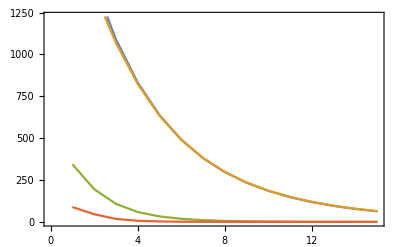

```mathematica
ListLinePlot[{JBL,JL,J2L,J3L},Frame->True,Axes->False]
```

This proves that the Wannier calculation is correct; as it agrees with the band structure calculation.

```mathematica
J21ratio=Table[{V0,Abs[J2[V0]]/Abs[J[V0]]},{V0,1,15,1}]
```

{{1,0.200969},{2,0.142308},{3,0.100677},{4,0.0715632},{5,0.0514028},{6,0.0373892},{7,0.0275492},{8,0.0205525},{9,0.0155117},{10,0.0118329},{11,0.00911487},{12,0.00708295},{13,0.00554624},{14,0.00436948},{15,0.00345447}}

```mathematica
J31ratio=Table[{V0,Abs[J3[V0]]/Abs[J[V0]]},{V0,1,15,1}]
```

{{1,0.0517782},{2,0.0333128},{3,0.016607},{4,0.00831113},{5,0.00425769},{6,0.00224068},{7,0.0012115},{8,0.000672154},{9,0.000382214},{10,0.000223012},{11,0.000134965},{12,0.0000883491},{13,0.0000696964},{14,0.0000758539},{15,0.000111937}}

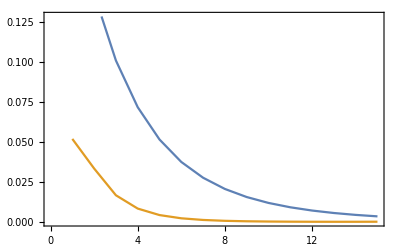

```mathematica
ListLinePlot[{J21ratio,J31ratio},Frame->True,Axes->False]
```

### Wannier U in 1 + 2 D

```mathematica
(*Third Lattice is assumed to be 20/25/30Er*)
```

```mathematica
IntW20=Module[{w3=wtab[[20]]},NIntegrate[Re[w3]^4,{x,-4*10^-6,4*10^-6}]]
IntW25=Module[{w3=wtab[[25]]},NIntegrate[Re[w3]^4,{x,-4*10^-6,4*10^-6}]]
IntW30=Module[{w3=wtab[[30]]},NIntegrate[Re[w3]^4,{x,-4*10^-6,4*10^-6}]]
```

6.89484×10^6

7.34338×10^6

7.72525×10^6

```mathematica
U1D=Table[Module[{wj},wj=wtab[[V0]];(4π hbar^2 150 a0)/(mK ErecoilKLattice)NIntegrate[Re[wj]^4,{x,-4*10^-6,4*10^-6}]*IntW20^2],{V0,1,20}];
```

```mathematica
U2D=Table[Module[{wj},wj=wtab[[V0]];(4π hbar^2 150 a0)/(mK ErecoilKLattice)NIntegrate[Re[wj]^4,{x,-4*10^-6,4*10^-6}]^2*IntW20],{V0,1,20}];
```

```mathematica
Table[{V,JB[V],U1D[[V]]*(ErecoilKLattice/h)/150/JB[V],U2D[[V]]*(ErecoilKLattice/h)/150/JB[V],Uw[[V]]*(ErecoilKLattice/h)/150/JB[V]},{V,1,20}]//MatrixForm
```

(1 | 1865.31 | 0.0117004 | 0.0045534 | 0.00177203
2 | 1428.69 | 0.0185034 | 0.00872221 | 0.0041115
3 | 1089.8 | 0.027761 | 0.0149762 | 0.00807915
4 | 831.744 | 0.0402485 | 0.0240255 | 0.0143415
5 | 637.178 | 0.0568475 | 0.036717 | 0.023715
6 | 490.894 | 0.0786096 | 0.0540906 | 0.0372193
7 | 380.702 | 0.106797 | 0.0774255 | 0.056132
8 | 297.306 | 0.142921 | 0.108288 | 0.0820467
9 | 233.792 | 0.188789 | 0.148582 | 0.116938
10 | 185.084 | 0.246548 | 0.200611 | 0.163233
11 | 147.463 | 0.318744 | 0.267147 | 0.223902
12 | 118.199 | 0.408384 | 0.351508 | 0.302552
13 | 95.28 | 0.519009 | 0.457651 | 0.403548
14 | 77.2138 | 0.654772 | 0.59028 | 0.53214
15 | 62.8848 | 0.820535 | 0.75496 | 0.694625
16 | 51.4542 | 1.02197 | 0.95826 | 0.898518
17 | 42.2857 | 1.26569 | 1.20791 | 1.15276
18 | 34.894 | 1.55937 | 1.51297 | 1.46795
19 | 28.9059 | 1.91188 | 1.88405 | 1.85662
20 | 24.0328 | 2.33352 | 2.33352 | 2.33352)

```mathematica
U2D20=Table[Module[{wj},wj=wtab[[V0]];(4π hbar^2 150 a0)/(mK ErecoilKLattice)NIntegrate[Re[wj]^4,{x,-4*10^-6,4*10^-6}]^2*IntW20],{V0,1,20}];
U2D25=Table[Module[{wj},wj=wtab[[V0]];(4π hbar^2 150 a0)/(mK ErecoilKLattice)NIntegrate[Re[wj]^4,{x,-4*10^-6,4*10^-6}]^2*IntW25],{V0,1,20}];
U2D30=Table[Module[{wj},wj=wtab[[V0]];(4π hbar^2 150 a0)/(mK ErecoilKLattice)NIntegrate[Re[wj]^4,{x,-4*10^-6,4*10^-6}]^2*IntW30],{V0,1,20}];
```

```mathematica
Table[{V,JB[V],Uw[[V]]*(ErecoilKLattice/h)/150/JB[V],U2D20[[V]]*(ErecoilKLattice/h)/150/JB[V],U2D25[[V]]*(ErecoilKLattice/h)/150/JB[V],U2D30[[V]]*(ErecoilKLattice/h)/150/JB[V]},{V,1,20}]//MatrixForm
```

(1 | 1865.31 | 0.00177203 | 0.0045534 | 0.00484962 | 0.00510181
2 | 1428.69 | 0.0041115 | 0.00872221 | 0.00928963 | 0.0097727
3 | 1089.8 | 0.00807915 | 0.0149762 | 0.0159504 | 0.0167799
4 | 831.744 | 0.0143415 | 0.0240255 | 0.0255884 | 0.0269191
5 | 637.178 | 0.023715 | 0.036717 | 0.0391056 | 0.0411392
6 | 490.894 | 0.0372193 | 0.0540906 | 0.0576094 | 0.0606052
7 | 380.702 | 0.056132 | 0.0774255 | 0.0824624 | 0.0867505
8 | 297.306 | 0.0820467 | 0.108288 | 0.115332 | 0.12133
9 | 233.792 | 0.116938 | 0.148582 | 0.158248 | 0.166477
10 | 185.084 | 0.163233 | 0.200611 | 0.213662 | 0.224772
11 | 147.463 | 0.223902 | 0.267147 | 0.284526 | 0.299322
12 | 118.199 | 0.302552 | 0.351508 | 0.374375 | 0.393843
13 | 95.28 | 0.403548 | 0.457651 | 0.487424 | 0.512771
14 | 77.2138 | 0.53214 | 0.59028 | 0.628681 | 0.661373
15 | 62.8848 | 0.694625 | 0.75496 | 0.804074 | 0.845887
16 | 51.4542 | 0.898518 | 0.95826 | 1.0206 | 1.07367
17 | 42.2857 | 1.15276 | 1.20791 | 1.28649 | 1.35339
18 | 34.894 | 1.46795 | 1.51297 | 1.61139 | 1.69519
19 | 28.9059 | 1.85662 | 1.88405 | 2.00661 | 2.11096
20 | 24.0328 | 2.33352 | 2.33352 | 2.48533 | 2.61457)

```mathematica
U1D20=Table[Module[{wj},wj=wtab[[V0]];(4π hbar^2 150 a0)/(mK ErecoilKLattice)NIntegrate[Re[wj]^4,{x,-4*10^-6,4*10^-6}]*IntW20^2],{V0,1,20}];
U1D25=Table[Module[{wj},wj=wtab[[V0]];(4π hbar^2 150 a0)/(mK ErecoilKLattice)NIntegrate[Re[wj]^4,{x,-4*10^-6,4*10^-6}]*IntW25^2],{V0,1,20}];
U1D30=Table[Module[{wj},wj=wtab[[V0]];(4π hbar^2 150 a0)/(mK ErecoilKLattice)NIntegrate[Re[wj]^4,{x,-4*10^-6,4*10^-6}]*IntW30^2],{V0,1,20}];
```

```mathematica
Table[{V,JB[V],Uw[[V]]*(ErecoilKLattice/h)/150/JB[V],U1D20[[V]]*(ErecoilKLattice/h)/150/JB[V],U1D25[[V]]*(ErecoilKLattice/h)/150/JB[V],U1D30[[V]]*(ErecoilKLattice/h)/150/JB[V]},{V,1,20}]//MatrixForm
```

(1 | 1865.31 | 0.00177203 | 0.0117004 | 0.0132723 | 0.0146885
2 | 1428.69 | 0.0041115 | 0.0185034 | 0.0209892 | 0.0232289
3 | 1089.8 | 0.00807915 | 0.027761 | 0.0314905 | 0.0348508
4 | 831.744 | 0.0143415 | 0.0402485 | 0.0456555 | 0.0505273
5 | 637.178 | 0.023715 | 0.0568475 | 0.0644845 | 0.0713655
6 | 490.894 | 0.0372193 | 0.0786096 | 0.0891701 | 0.0986852
7 | 380.702 | 0.056132 | 0.106797 | 0.121144 | 0.134071
8 | 297.306 | 0.0820467 | 0.142921 | 0.162121 | 0.179421
9 | 233.792 | 0.116938 | 0.188789 | 0.214151 | 0.237002
10 | 185.084 | 0.163233 | 0.246548 | 0.279669 | 0.309512
11 | 147.463 | 0.223902 | 0.318744 | 0.361565 | 0.400146
12 | 118.199 | 0.302552 | 0.408384 | 0.463248 | 0.512679
13 | 95.28 | 0.403548 | 0.519009 | 0.588734 | 0.651556
14 | 77.2138 | 0.53214 | 0.654772 | 0.742735 | 0.82199
15 | 62.8848 | 0.694625 | 0.820535 | 0.930768 | 1.03009
16 | 51.4542 | 0.898518 | 1.02197 | 1.15927 | 1.28297
17 | 42.2857 | 1.15276 | 1.26569 | 1.43573 | 1.58893
18 | 34.894 | 1.46795 | 1.55937 | 1.76885 | 1.9576
19 | 28.9059 | 1.85662 | 1.91188 | 2.16873 | 2.40015
20 | 24.0328 | 2.33352 | 2.33352 | 2.64701 | 2.92946)